# EIWL Sections 43, 44

## Section 43

## Section 44

## 4/4 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

```mathematica
Import["https://www.google.com","Images"]
```

{-Graphics-}

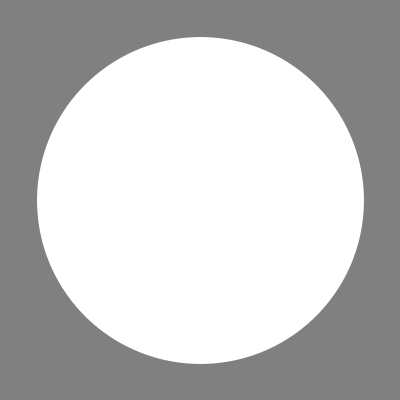
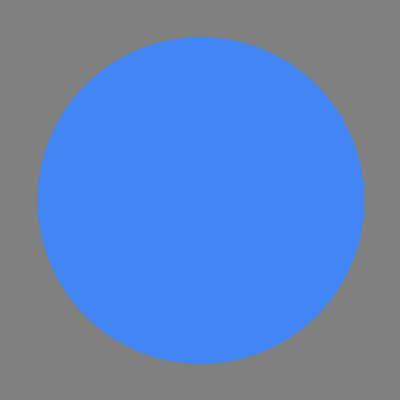
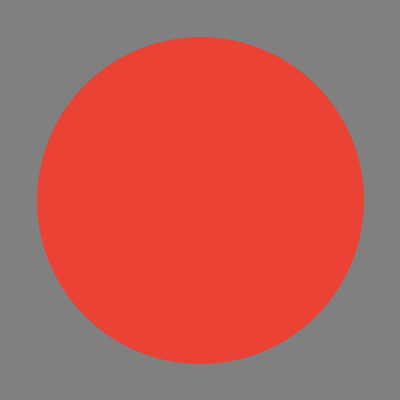
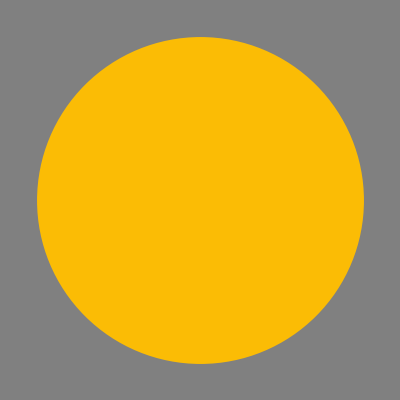
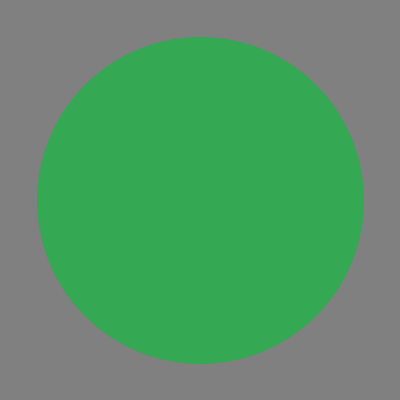

```mathematica
Graphics[Style[Disk[],#],Background->Gray]&/@DominantColors[-Graphics-]
```

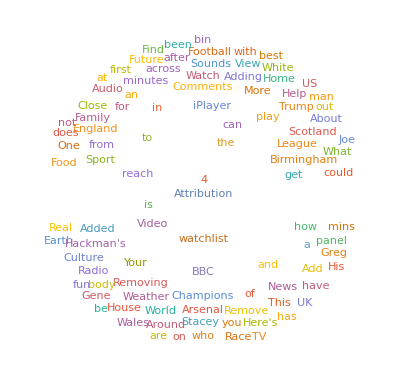

```mathematica
WordCloud[TextWords[Import["https://bbc.co.uk"]]]
```

```mathematica
ImageCollage[Import["https://nps.gov","Images"]]
```

-Graphics-

```mathematica
If[ImageInstanceQ[#,"bird"],#,Nothing]&/@Import["https://en.wikipedia.org/wiki/Ostrich","Images"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WordCloud[TextCases[Import["https://www.nato.int"],"Country"]]
```

-Graphics-

```mathematica
Import["https://www.nato.int"]
```

Access Denied  You don't have permission to access "http://www.nato.int/" on this server.
 Reference #18.340c3417.1744844100.6209642 
https://errors.edgesuite.net/18.340c3417.1744844100.6209642

```mathematica
Length[Import["https://en.wikipedia.org","Hyperlinks"]]
```

370

```mathematica
SendMail["yonago@deepsprings.edu",{-Graphics-}]
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Success[…]

```mathematica
SendMail["yonago@deepsprings.edu",MoonPhase["Icon"]]
```

Success[…]